# Derive pressure volume relationship for an elastic sphere

With both linearized strains (like from Knoche and Kierfeld (KK)) and non-linearized strains (like surface evolver, apparently)

The energy density is (from KK)

```mathematica
ws=1/2 eh0/(1-ν^2)(es^2+2ν es eϕ +eϕ^2)
```

(eh0 (es^2+eϕ^2+2 es eϕ ν))/(2 (1-ν^2))

For a sphere, the strains are the same everywhere and in all directions

```mathematica
wssphere=ws/.{eϕ->e,es->e}//Simplify
```

(e^2 eh0)/(1-ν)

## Linear linearization: e=λ-1

The energy density with the linearization from KK

```mathematica
wskk=wssphere/.e->λ-1
```

(eh0 (-1+λ)^2)/(1-ν)

The we find the enthalpy (integrals are done over the unstrained sphere)

```mathematica
gkk=4π r0^2 wskk-p 4/3 π r0^3 λ^3
```

-4/3 p π r0^3 λ^3+(4 eh0 π r0^2 (-1+λ)^2)/(1-ν)

Minimize

```mathematica
gkksol=Solve[D[gkk,λ]==0,λ]
```

{{λ→-(-(8 eh0)/(1-ν)-(8 √(eh0^2-2 eh0 p r0+2 eh0 p r0 ν))/(√(1-2 ν+ν^2)))/(8 p r0)},{λ→-(-(8 eh0)/(1-ν)+(8 √(eh0^2-2 eh0 p r0+2 eh0 p r0 ν))/(√(1-2 ν+ν^2)))/(8 p r0)}}

Find the right branch

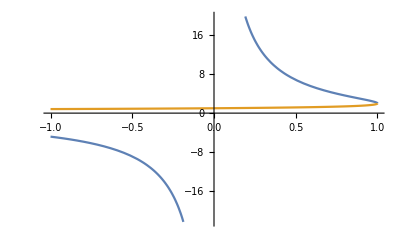

```mathematica
Plot[λ/.gkksol/.{eh0->1,r0->1,ν->.5}//Evaluate,{p,-1,1}]
```

Must be the second branch. Then the strained radius is

```mathematica
kksol=r0 λ/.gkksol[[2]]//Expand
```

eh0/(p (1-ν))-(√(eh0^2-2 eh0 p r0+2 eh0 p r0 ν))/(p √(1-2 ν+ν^2))

This should agree with the solution given in the paper

```mathematica
kkpapersol=Solve[r^2-2eh0/(p(1-ν))(r-r0)==0,r]
```

{{r→1/2 (-√((4 eh0^2)/(p^2 (1-ν)^2)-(8 eh0 r0)/(p (1-ν)))+(2 eh0)/(p (1-ν)))},{r→1/2 (√((4 eh0^2)/(p^2 (1-ν)^2)-(8 eh0 r0)/(p (1-ν)))+(2 eh0)/(p (1-ν)))}}

```mathematica
kksol==r/.kkpapersol[[1]]//Simplify
```

(-p √((eh0 (eh0+2 p r0 (-1+ν)))/(p^2 (-1+ν)^2))+(√(eh0 (eh0+2 p r0 (-1+ν))))/(√((-1+ν)^2)))/p==0

## non-linear linearization e=(λ^2-1)/2

These agree when λ is close to 1

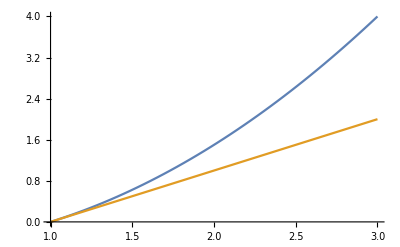

```mathematica
Plot[{(λ^2-1)/2,λ-1},{λ,1,3}]
```

The energy density with this relationship is

```mathematica
wsse=wssphere/.e->(λ^2-1)/2//Simplify
```

-(eh0 (-1+λ^2)^2)/(4 (-1+ν))

```mathematica
gse=4π r0^2 wsse-p 4/3 π r0^3 λ^3
```

-4/3 p π r0^3 λ^3-(eh0 π r0^2 (-1+λ^2)^2)/(-1+ν)

Which gives us an minimum enthalpy at

```mathematica
gsesol=Solve[D[gse,λ]==0,λ]//Simplify
```

{{λ→0},{λ→((-p r0+√((4 eh0^2+p^2 r0^2 (-1+ν)^2)/(-1+ν)^2)) (-1+ν))/(2 eh0)},{λ→((4 p r0+√(16 p^2 r0^2+(64 eh0^2)/(-1+ν)^2)) (1-ν))/(8 eh0)}}

Which branch?

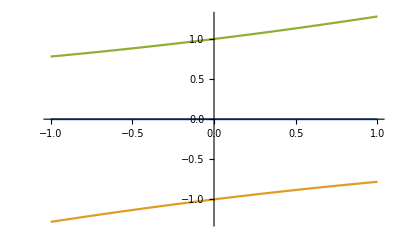

```mathematica
Plot[λ/.gsesol/.{eh0->1,r0->1,ν->.5}//Evaluate,{p,-1,1}]
```

The third one must be correct, so the solution for the strained radius is

```mathematica
sesol=r0 λ/.gsesol[[3]]//FullSimplify
```

-(r0 (p r0+√(p^2 r0^2+(4 eh0^2)/(-1+ν)^2)) (-1+ν))/(2 eh0)

## Comparison

Plot the radii together

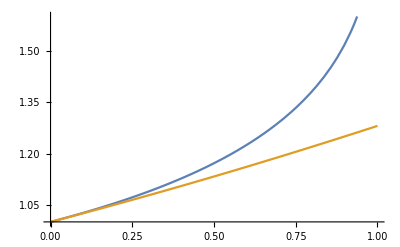

```mathematica
Plot[{kksol,sesol}/.{eh0->1,r0->1,ν->.5}//Evaluate,{p,0,1}]
```

And the volumes

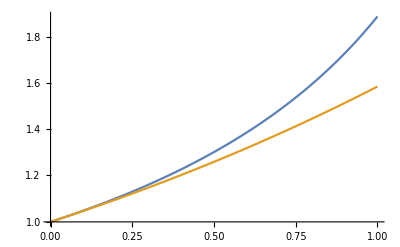

```mathematica
Plot[4/3π r^3/.r->{kksol,sesol}/.{eh0->1,r0->.62,ν->.5}//Evaluate,{p,0,1}]
```